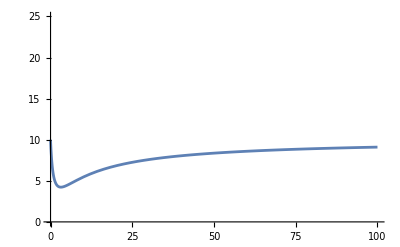

```mathematica
k=10;
Plot[k*(t+k*1/(t+1))/(t+k),{t,0,100},PlotRange->{{0,100},{0,25}}]
```

```mathematica
Clear["Global`*"]
syst = {
s'[t]==-beta*k*(t+k*1/(t+1))/(t+k)*s[t]*i[t]+gamma*r[t],
p'[t]==beta*k*(t+k*1/(t+1))/(t+k)*s[t]*i[t]-beta*k*(t+k*1/(t+1))/(t+k)*s[t-tau]*i[t-tau],
i'[t]==beta*k*(t+k*1/(t+1))/(t+k)*s[t-tau]*i[t-tau]-(mu+d)*i[t],
r'[t]==mu*i[t]-gamma*r[t], 
r[0]==0,
i[0]==i0,
p[0]==k*i[0],
s[0]==1-p[0]-i[0]
};
ssol=ParametricNDSolveValue[syst, {s[t],i[t],r[t],p[t]}, {t,0,100},{beta, mu, i0, d, gamma,k,tau}]
Manipulate[Plot[{
ssol[beta, mu, i0, d, gamma,k,tau][[1]],
ssol[beta, mu, i0, d, gamma,k,tau][[2]],
ssol[beta, mu, i0, d, gamma,k,tau][[3]],
ssol[beta, mu, i0, d, gamma,k,tau][[4]]},{t,0,100},
PlotStyle->{Blue, Red,Orange,Green},
FrameStyle->Directive[Black,15],Frame->True, FrameLabel->{
Style["t",20,Black,FontFamily->"Cambria"],
Style["s[t],i[t],r[t]",20,Black,FontFamily->"Cambria"]},
GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],
PlotRange->Automatic,PlotLegends->Placed[{
Style["s[t]",20,Black,FontFamily->"Cambria"],
Style["i[t]",20,Black,FontFamily->"Cambria"],
Style["r[t]",20,Black,FontFamily->"Cambria"],
Style["e[t]",20,Black,FontFamily->"Cambria"]},Right],ImageSize->512],
{{beta, 0.2},0,1}, 
{{mu,0.2},0,1}, 
{{gamma,2*10^-4},0,0.2},
{{d,5*10^-3},0,0.01},
{{k,6},0,10},
{{tau,5},0,10},
{{i0,  0.001}, 0, 0.01}]
```

ParametricFunction[<>]

0.05

ParametricFunction[<>]

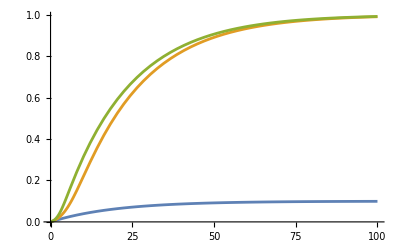

```mathematica
Clear["Global`*"]
mu=0.05
sol=ParametricNDSolveValue[{
s'[t]==-b *s[t]* i[t],
i'[t]==b *s[t] *i[t]-mu* i[t],
r'[t]==mu *i[t],
s[0]==1-r[0]-i[0],
i[0]==0.1,
r[0]==0},
{s[t],i[t],r[t]},{t,0,100},{b}]
Plot[Evaluate[Table[sol[b][[3]],{b,0,1,0.5}]],{t,0,100},PlotRange->All]
```